```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]<>"\\Code\\OutputData"];
```

# Создание таблиц

## Модуль для вычисления абсолютной ошибки

```mathematica
(* Функция, возращающая абсолютную ошибку сетки*)
AbsErr[data_, sol_]:=Module[{maxError},
maxError =Max@Table[Abs[data[[2]][[i]]- (sol/.{x->data[[1]][[i]]})],{i,1,Length[data[[1]]]}];
{maxError}
]
```

## Модуль для вычисления относительной ошибки

```mathematica
(*Функция, охрененно обрезающая массив *)
ResizeData[data_, step1_ : 1, step2_: 1] := Module[{newdata},
newdata =Join[
{Join[{data[[1]][[1]]},Table[data[[1]][[j]], {j, 2, Length@data[[1]], step1}]]},
Table[Join[{data[[i]][[1]]},Table[data[[i]][[j]], {j, 2, Length@data[[1]], step1}]], {i, 2, Length@data, step2}]];
newdata
]
```

```mathematica
SizeData[data_] := Module[{},
Print[{Length@data, Length@data[[1]]}]
]
```

```mathematica
(* Функция, возращающая относительную ошибку сеток*)
EstErr[data1_,data2_]:=Module[{maxError, curError},
maxError=0;
curError=0;

For[i=1,i<Min[Length[data1[[2]]], Length[data2[[2]]]]-1,i++,

curError=Abs[data1[[2]][[i]]- data2[[2]][[i]]];
If[curError>maxError,maxError=curError;];
(*Print[curError]*)
];
{maxError}
]
```

## Модуль для создания таблиц

```mathematica
(* Модуль для создания таблиц *)
CreateTable[globalTable_, truesolve_, h0_, hstep_]:=Module[{hx,hy,n, grid1Data ,gr11},
(*globalTable = {table1,table2,table3,table4,table5};*)
TableAbsErr = Table[AbsErr[globalTable[[i]], sol][[1]], {i, 1, Length@globalTable}];
TableEstErr = Table[EstErr[globalTable[[i]], globalTable[[i-1]]][[1]], {i, 2, Length@globalTable}];
hx =hx0;
hy= hy0;

tabLabel={"h_x", "Норма ошибки на точном решении", "Порядок сходимости на точном решении", "Норма ошибки по правилу Эйткена", "Порядок сходимости по правилу Эйткена"};
n = Length@globalTable;
tab1Data=Table[Table[{},{j,1,Length[tabLabel]}],{i,1,n}];
tab1Data[[1,3]] = "-";
tab1Data[[1,4]] = "-";
tab1Data[[1,5]] = "-";
tab1Data[[2,5]] = "-";

For[i = 1, i<=n,i++,tab1Data[[i,1]]={h0/hstep^(i-1)}];
For[i = 1, i<=n,i++,tab1Data[[i,2]]= TableAbsErr[[i]]];
For[j = 2, j<=n,j++,tab1Data[[j,3]]= Log[2, tab1Data[[j-1,2]]/tab1Data[[j,2]]]];
For[j = 2, j<=n,j++,tab1Data[[j,4]]= TableEstErr[[j-1]]];
For[j = 3, j<=n,j++,tab1Data[[j,5]]= Log[2, tab1Data[[j-1,4]]/tab1Data[[j,4]]]];
grid1Data={tabLabel}~Join~tab1Data;
gr11 = Grid[grid1Data,Frame->All]
]
```

## Пример таблички для метода квадратур

```mathematica
(*Инфо о файлах *) 
stepH= 2;
data1 = Import["data_for_tables\\QuadtratureTest_0.txt", "Table"];
(*data1 = Most[data1];*) (* Удалили последний элемент для нужного числа *)
SizeData[data1];

data2 = Import["data_for_tables\\QuadtratureTest_1.txt", "Table"];
data2 = ResizeData[data2, stepH];
SizeData[data2];

data3= Import["data_for_tables\\QuadtratureTest_2.txt", "Table"];
data3 = ResizeData[data3, stepH^2];
SizeData[data3];

data4 = Import["data_for_tables\\QuadtratureTest_3.txt", "Table"];
data4 = ResizeData[data4, stepH^3];
SizeData[data4];

data5 = Import["data_for_tables\\QuadtratureTest_4.txt", "Table"];
data5 = ResizeData[data5, stepH^4];
SizeData[data5];

data6 = Import["data_for_tables\\QuadtratureTest_5.txt", "Table"];
data6 = ResizeData[data6, stepH^5];
SizeData[data6];
DATA = {data1, data2, data3, data4, data5, data6};
```

{2,11}

{2,11}

{2,11}

«3 more identical outputs»

```mathematica
sol = 1;
CreateTable[DATA, sol, 0.1, 2]
```

h_x | Норма ошибки на точном решении | Порядок сходимости на точном решении | Норма ошибки по правилу Эйткена | Порядок сходимости по правилу Эйткена
{0.1} | 0.000469858 | - | - | -
{0.05} | 0.000092428 | 2.34582 | 0.000235627 | -
{0.025} | 0.0000202879 | 2.18771 | 0.0000425629 | 2.46884
{0.0125} | 4.73934×10^-6 | 2.09786 | 8.89669×10^-6 | 2.25826
{0.00625} | 1.1445×10^-6 | 2.04997 | 2.02445×10^-6 | 2.13574
{0.003125} | 2.8116×10^-7 | 2.02525 | 4.82271×10^-7 | 2.06961

Вопрос №8

```mathematica
sol = Log[x]-(2ⅇ)/x;
Qdata1 = Import["QuadCheck3.txt","Table"];
AbsErr[Qdata1, sol]
```

{0.121362}

Вопрос №9

```mathematica
(*Найдём множитель q*)
λ9 = 1/(2π);
K9[x_,s_]:=s Sin[x];
q9 = Abs[λ9]FindMaximum[Integrate[K9[x,s], {s, 0, π}], {x,0,π}][[1]];
```

```mathematica
"string №"  <>ToString[1];
sol9 = Cos[x]-2/π Sin[x];
Tab9AbsError = Table[AbsErr[Import["StopCriterionCheck" <> ToString[i]<>".txt","Table"],sol9],{i,1,12}];
Tab9Its = Table[Import["StopCriterionCheck" <> ToString[i]<>".txt","Table"][[3]],{i,1,12}];
Grid9Label = {"Число итераций", "Норма ошибки на точном решении", "Теоретическая ошибка"};
(*Априорная оценка погрешности по нач. приближению и результату на k-й итерации*)
f9 = Cos[x];
Tab9ThEr = Table[q9^k/(1-q9^k)AbsErr[Import["StopCriterionCheck" <> ToString[i]<>".txt","Table"],f9],{k,1,12}];
Grid9Data = Transpose[{Flatten@Tab9Its,Flatten@Tab9AbsError, Flatten@Tab9ThEr}];
Grid9Data={Grid9Label}~Join~Grid9Data;
Grid9 = Grid[Grid9Data,Frame->All]
```

Число итераций | Норма ошибки на точном решении | Теоретическая ошибка
1 | 0.302813 | 2.38235
2 | 0.139675 | 1.048
3 | 0.0612216 | 0.61174
4 | 0.027017 | 0.399825
5 | 0.0195117 | 0.27745
6 | 0.0219259 | 0.199648
7 | 0.0243869 | 0.14712
8 | 0.025814 | 0.110202
9 | 0.026555 | 0.0835185
10 | 0.0269275 | 0.0638376
11 | 0.0271101 | 0.0491045
12 | 0.0272009 | 0.0379522

Вопрос №10

Число слагаемых в замене ядра | Норма ошибки на точном решении | Число обусловленности
3 | 0.0200134 | 3.24787
4 | 0.0035457 | 4.34116
5 | 0.000527395 | 5.4308
6 | 0.000103832 | 6.45556
7 | 0.0000274986 | 7.4106
8 | 0.000016259 | 8.30306
9 | 0.000014936 | 9.1408
10 | 0.0000149081 | 9.93064
11 | 0.0000149068 | 10.6782
12 | 0.0000149068 | 11.3883
13 | 0.0000149068 | 12.0649
14 | 0.0000149068 | 12.7113
15 | 0.0000149068 | 13.3304
16 | 0.0000149068 | 13.9246
17 | 0.0000149068 | 14.4963
18 | 0.0000149068 | 15.0471
19 | 0.0000149068 | 15.5788
20 | 0.0000149068 | 16.0928
21 | 0.0000149068 | 16.5904
22 | 0.0000149068 | 17.0727
23 | 0.0000149068 | 17.5408
24 | 0.0000149068 | 17.9956
25 | 0.0000149068 | 18.4379
26 | 0.0000149068 | 18.8686
27 | 0.0000149068 | 19.2881
28 | 0.0000149068 | 19.6973
29 | 0.0000149068 | 20.0967
30 | 0.0000149068 | 20.4867
31 | 0.0000149068 | 20.8679
32 | 0.0000149068 | 21.2408
33 | 0.0000149068 | 21.6057
34 | 0.0000149068 | 21.963
35 | 0.0000149068 | 22.3131
36 | 0.0000149068 | 22.6563
37 | 0.0000149068 | 22.993
38 | 0.0000149068 | 23.3233
39 | 0.0000149068 | 23.6476
40 | 0.0000149068 | 23.9661
41 | 0.0000149068 | 24.279
42 | 0.0000149068 | 24.5866
43 | 0.0000149068 | 24.8891
44 | 0.0000149068 | 25.1867
45 | 0.0000149068 | 25.4796
46 | 0.0000149068 | 25.7678
47 | 0.0000149068 | 26.0517
48 | 0.0000149068 | 26.3314
49 | 0.0000149068 | 26.6069
50 | 0.0000149068 | 26.8785
51 | 0.0000149068 | 27.1462
52 | 0.0000149068 | 27.4102
53 | 0.0000149068 | 27.6707
54 | 0.0000149068 | 27.9277
55 | 0.0000149068 | 28.1813
56 | 0.0000149068 | 28.4317
57 | 0.0000149068 | 28.679
58 | 0.0000149068 | 28.9231
59 | 0.0000149068 | 29.1643
60 | 0.0000149068 | 29.4027
61 | 0.0000149068 | 29.6382
62 | 0.0000149068 | 29.871
63 | 0.0000149068 | 30.1011
64 | 0.0000149068 | 30.3287
65 | 0.0000149068 | 30.5538
66 | 0.0000149068 | 30.7764
67 | 0.0000149068 | 30.9966
68 | 0.0000149068 | 31.2146
69 | 0.0000149068 | 31.4303
70 | 0.0000149068 | 31.6438
71 | 0.0000149068 | 31.8552
72 | 0.0000149068 | 32.0644
73 | 0.0000149068 | 32.2717
74 | 0.0000149068 | 32.4769
75 | 0.0000149068 | 32.6803
76 | 0.0000149068 | 32.8817
77 | 0.0000149068 | 33.0813
78 | 0.0000149068 | 33.279
79 | 0.0000149068 | 33.4751
80 | 0.0000149068 | 33.6693
81 | 0.0000149068 | 33.862
82 | 0.0000149068 | 34.0529
83 | 0.0000149068 | 34.2423
84 | 0.0000149068 | 34.43
85 | 0.0000149068 | 34.6163
86 | 0.0000149068 | 34.801
87 | 0.0000149068 | 34.9843
88 | 0.0000149068 | 35.1661
89 | 0.0000149068 | 35.3465
90 | 0.0000149068 | 35.5255
91 | 0.0000149068 | 35.7031
92 | 0.0000149068 | 35.8794
93 | 0.0000149068 | 36.0545
94 | 0.0000149068 | 36.2282
95 | 0.0000149068 | 36.4007
96 | 0.0000149068 | 36.572
97 | 0.0000149068 | 36.742
98 | 0.0000149068 | 36.9109
99 | 0.0000149068 | 37.0786

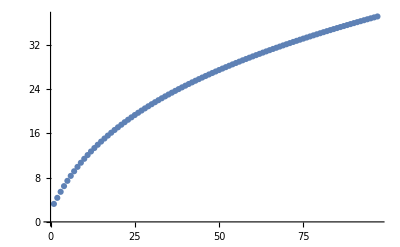

```mathematica
sol10 =x^3;
FullSimplify[sol10 - (4*Integrate[x^2 ⅇ^(x^2 s^4) (sol10/.x->s),{s,0,1}]+x^3-(ⅇ^(x^2)-1))];
series = x^2+ Sum[(x^(2(k+1))s^(4k))/(k!),{k,1,4}];
Tab10AbsError = Table[AbsErr[Import["DegenerateTest2_" <> ToString[i]<>".txt","Table"],sol10],{i,3,99}];
Tab10Condas = Table[Import["DegenerateTest2_" <> ToString[i]<>".txt","Table"][[3]],{i,3,99}];
Grid10Data = Transpose[{Table[i,{i,3,99}],Flatten@Tab10AbsError,Flatten@ Tab10Condas}];
Grid10Label = {"Число слагаемых в замене ядра", "Норма ошибки на точном решении", "Число обусловленности"};
Grid10Data={Grid10Label}~Join~Grid10Data;
Grid10 = Grid[Grid10Data,Frame->All]
ListPlot[Flatten@Tab10Condas]
```

Вопрос №12

```mathematica
Tab11Rs = Table[Import["SingularTest3_" <> ToString[i]<>".txt","Table"][[3]],{i,1,6}];
Grid11Data = Transpose[{Table[i,{i,1,6}],Flatten@Tab11Rs}];
Grid11Label = {"Число контрольных точек", "R"};
Grid11Data={Grid11Label}~Join~Grid11Data;
Grid11 = Grid[Grid11Data,Frame->All]
```

Число контрольных точек | R
1 | 1.57282×10^-16
2 | 6.15669×10^-16
3 | -5.89806×10^-17
4 | -8.10529×10^-16
5 | -1.36643×10^-16
6 | -2.75765×10^-16